Generate simulation data over the following regime of input parameters
constant:
	alpha=2
	length=8
	randomstart=True
	samples=100
raning
	colors=8,10,12,14,16
	power=0,0.5,2,3

```mathematica
data = 
With[
{alpha=2,
length=8,
randomstart=True,
samples=1000,
mode="data"},
ParallelTable[Clusters2[alpha,length,colors,power,randomstart,samples,mode],
{colors,8,80,8},
{power, 0,4,0.1}]] // (Flatten[#,2]&);
```

```mathematica
data2 = 
With[
{alpha=2,
length=8,
randomstart=True,
samples=1000,
mode="data"},
ParallelTable[Clusters2[alpha,length,colors,power,randomstart,samples,mode],
{colors,2,20,2},
{power, 0,4,0.1}]] // (Flatten[#,2]&)
```

{{2,8,2,0,135,120,1,502,0.535185},{2,8,2,0,131,124,1,514,0.509542},{2,8,2,0,114,140,1,508,0.442982},{2,8,2,0,125,130,1,544,0.456},{2,8,2,0,135,121,1,492,0.544444},{2,8,2,0,126,130,1,476,0.527778},{2,8,2,0,142,114,1,506,0.554577},{2,8,2,0,131,124,1,504,0.519084},{2,8,2,0,127,128,1,508,0.5},{2,8,2,0,141,115,1,498,0.558511},{2,8,2,0,119,136,1,518,0.455882},{2,8,2,0,126,128,1,528,0.47619},{2,8,2,0,125,131,1,492,0.508},{2,8,2,0,122,132,1,494,0.493852},«409972»,{2,8,20,4,230,26,5,192,0.895652},{2,8,20,4,237,19,2,144,0.924051},{2,8,20,4,235,21,3,150,0.920213},{2,8,20,4,238,18,3,138,0.927521},{2,8,20,4,234,22,4,160,0.91453},{2,8,20,4,238,18,4,128,0.932773},{2,8,20,4,234,22,4,162,0.913462},{2,8,20,4,251,5,3,40,0.98008},{2,8,20,4,238,18,3,136,0.928571},{2,8,20,4,1,8,2,8,0},{2,8,20,4,237,19,4,142,0.925105},{2,8,20,4,238,18,5,142,0.92542},{2,8,20,4,238,18,3,130,0.931723},{2,8,20,4,235,21,3,154,0.918085}}

```mathematica
Length[data]
```

410000

Now

```mathematica
With[{colors=14},
With[
{k0    = data //FilterByCol["m",colors,#] & // FilterByCol["k",0,#]&,
k01 = data //FilterByCol["m",colors,#] & // FilterByCol["k",0.1,#]&,
k2 = data //FilterByCol["m",colors,#] & // FilterByCol["k",2,#]&},
Histogram3D[
{SelectCols["E","r",k0],
SelectCols["E","r",k2],
SelectCols["E","r",data //FilterByCol["m",8,#] & // FilterByCol["k",3,#]&]}
,AxesLabel->{"E","r"}]]]
```

-Graphics3D-

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

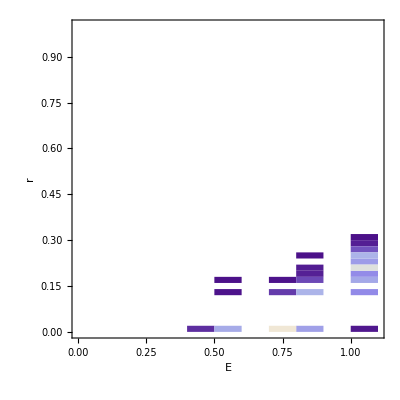
{4.017676,-Graphics-}

```mathematica
With[{m=8,k=0},
DensityHistogram[
 Map[List[(#⟦1⟧/(m-1)),(#⟦2⟧)] &, 
SelectCols["E","r",data // FilterByCol["m",m,#]& // FilterByCol["k",k,#]&]
] 
,
PlotRange->{{0,1.1},{0,1}} ,
AxesLabel->{"E","r"}
]] // AbsoluteTiming
```

In the grid below, k is increasing from left to right, and m is increasing from top to bottom.

Within each grid cell, E is increasing from left to right, and r is increasing from bottom to top

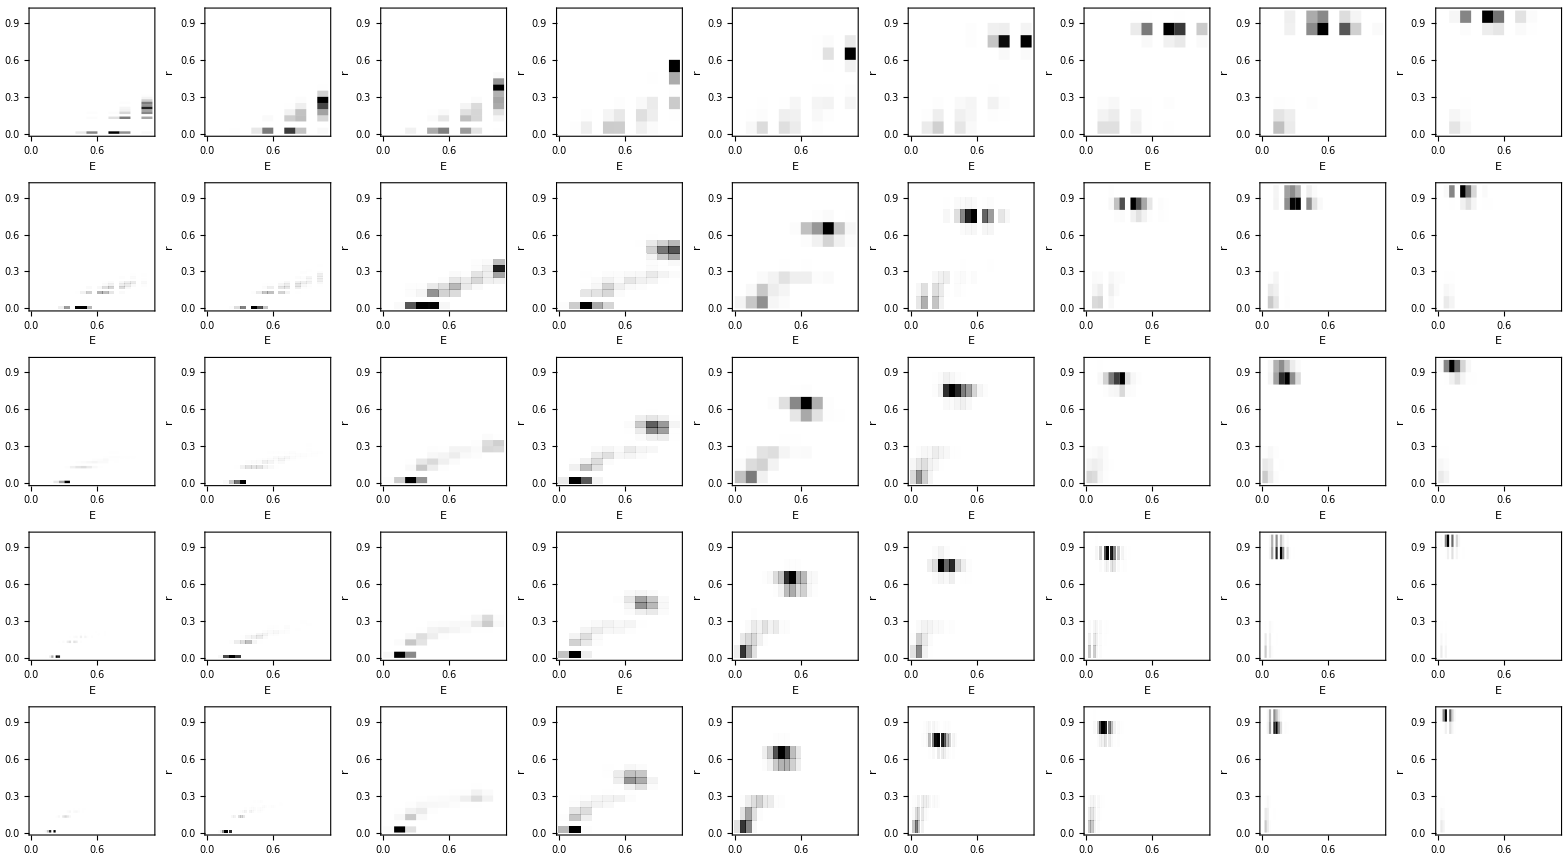

```mathematica
GraphicsGrid[Table[
With[{m=m,k=k},
DensityHistogram[
 Map[List[(#⟦1⟧/(m-1)),(#⟦2⟧)] &, 
SelectCols["E","r",data // FilterByCol["m",m,#]& // FilterByCol["k",k,#]&]
]
,
PlotRange->{{0,1.1},{0,1}} ,
AxesLabel->{"E","r"},
ColorFunction->Function[{height},Opacity[height]],
ChartBaseStyle->Black,
PerformanceGoal->"Speed"]
]
,
{m,8,40,8},{k,0,4,0.5}]]
```

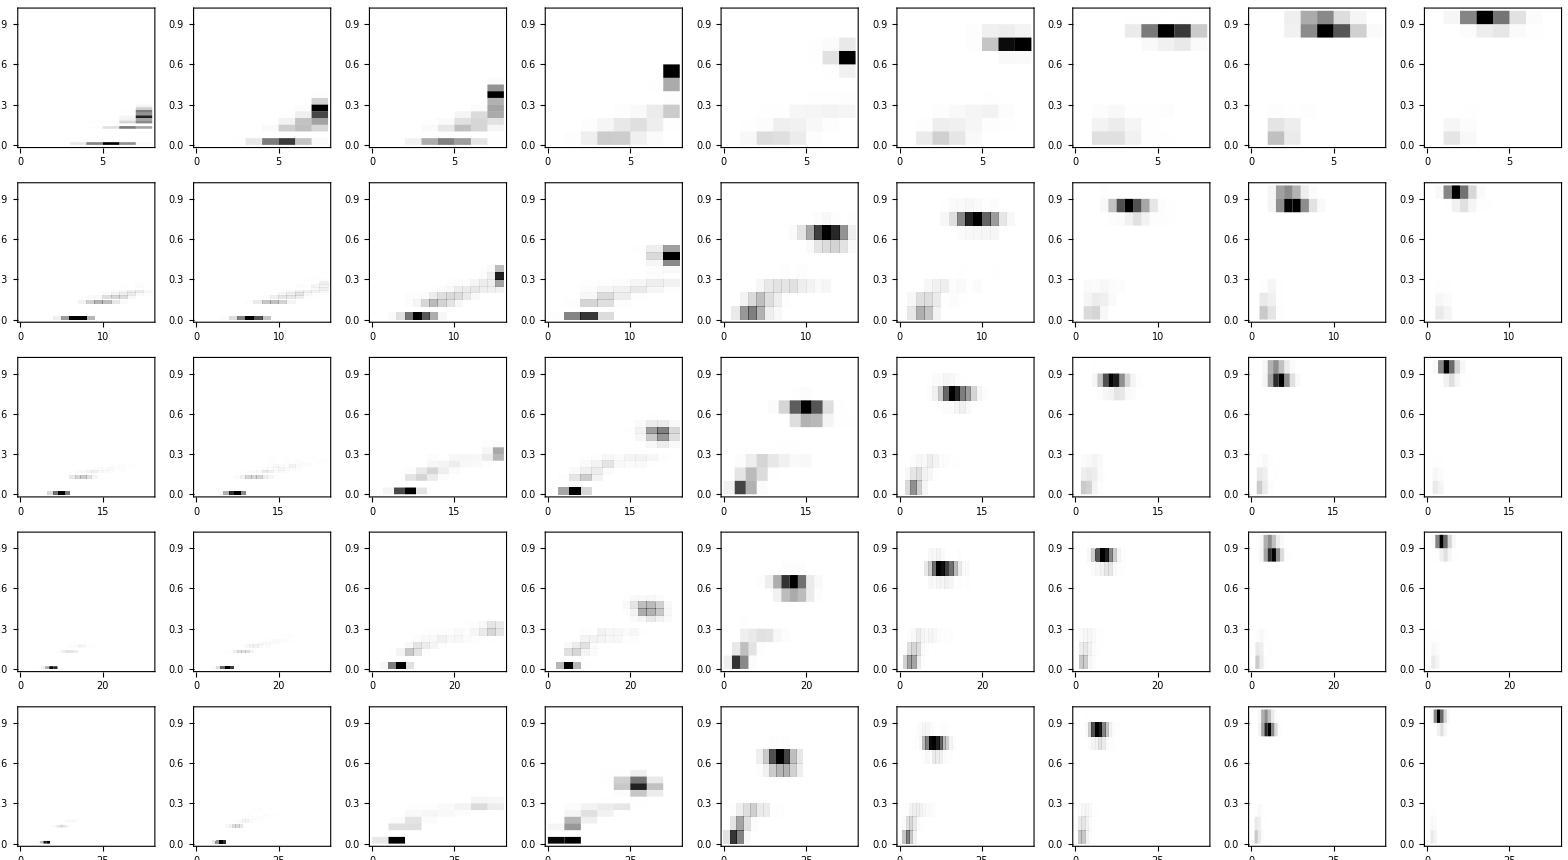

```mathematica
With[{dataframe=data},
GraphicsGrid[Table[
EmbeddableHeatmapEvsr[m,k,dataframe],
{m,8,40,8},{k,0,4,0.5}]]]
```

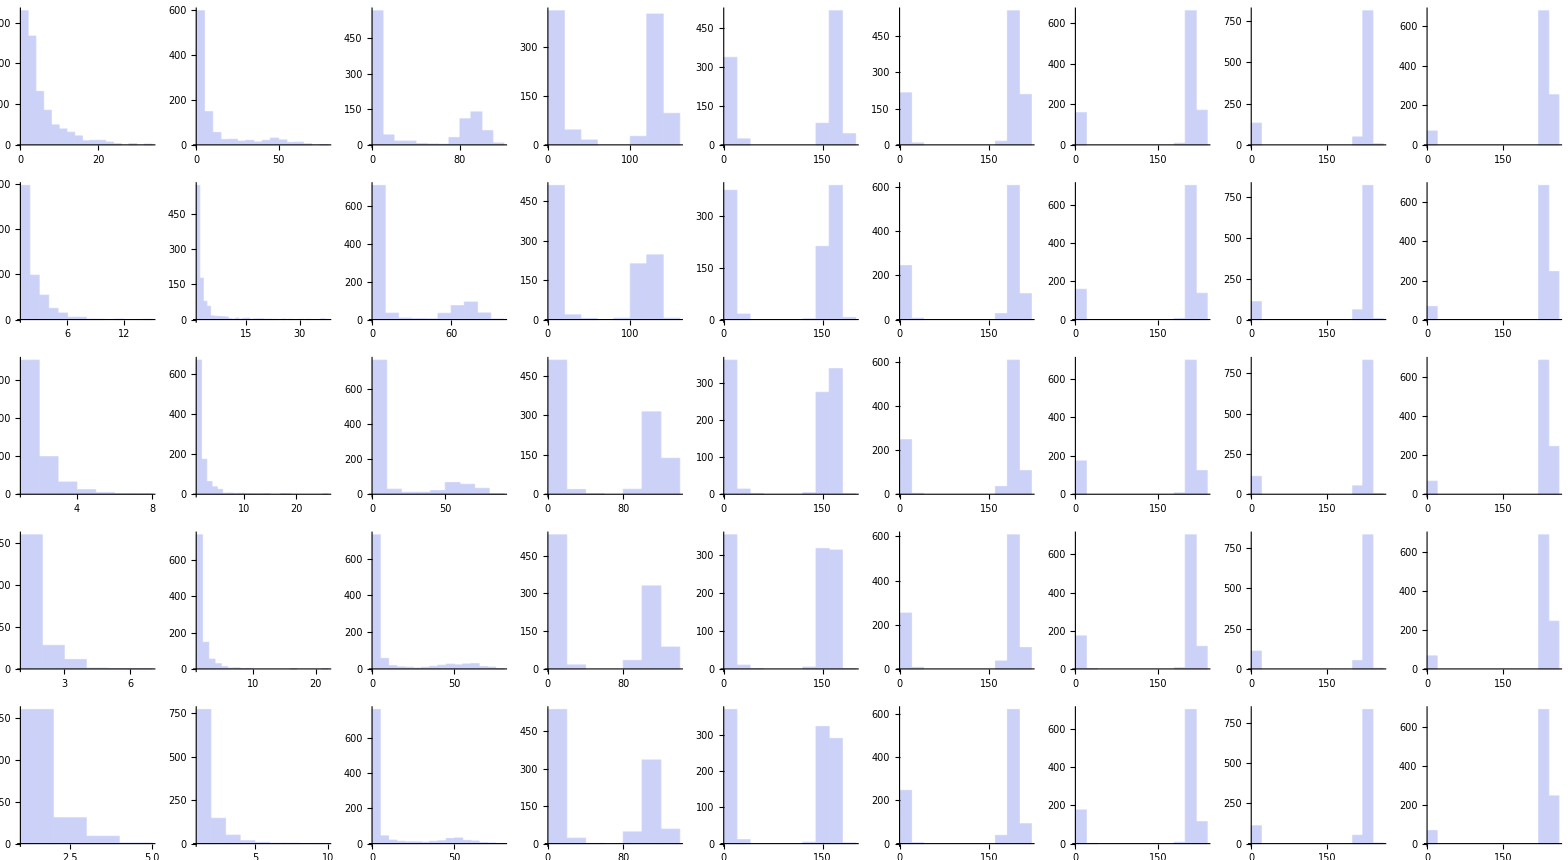

```mathematica
With[{dataframe=data},
GraphicsGrid[Table[
HistogramS[m,k,dataframe],
{m,8,40,8},{k,0,4,0.5}]]]
```

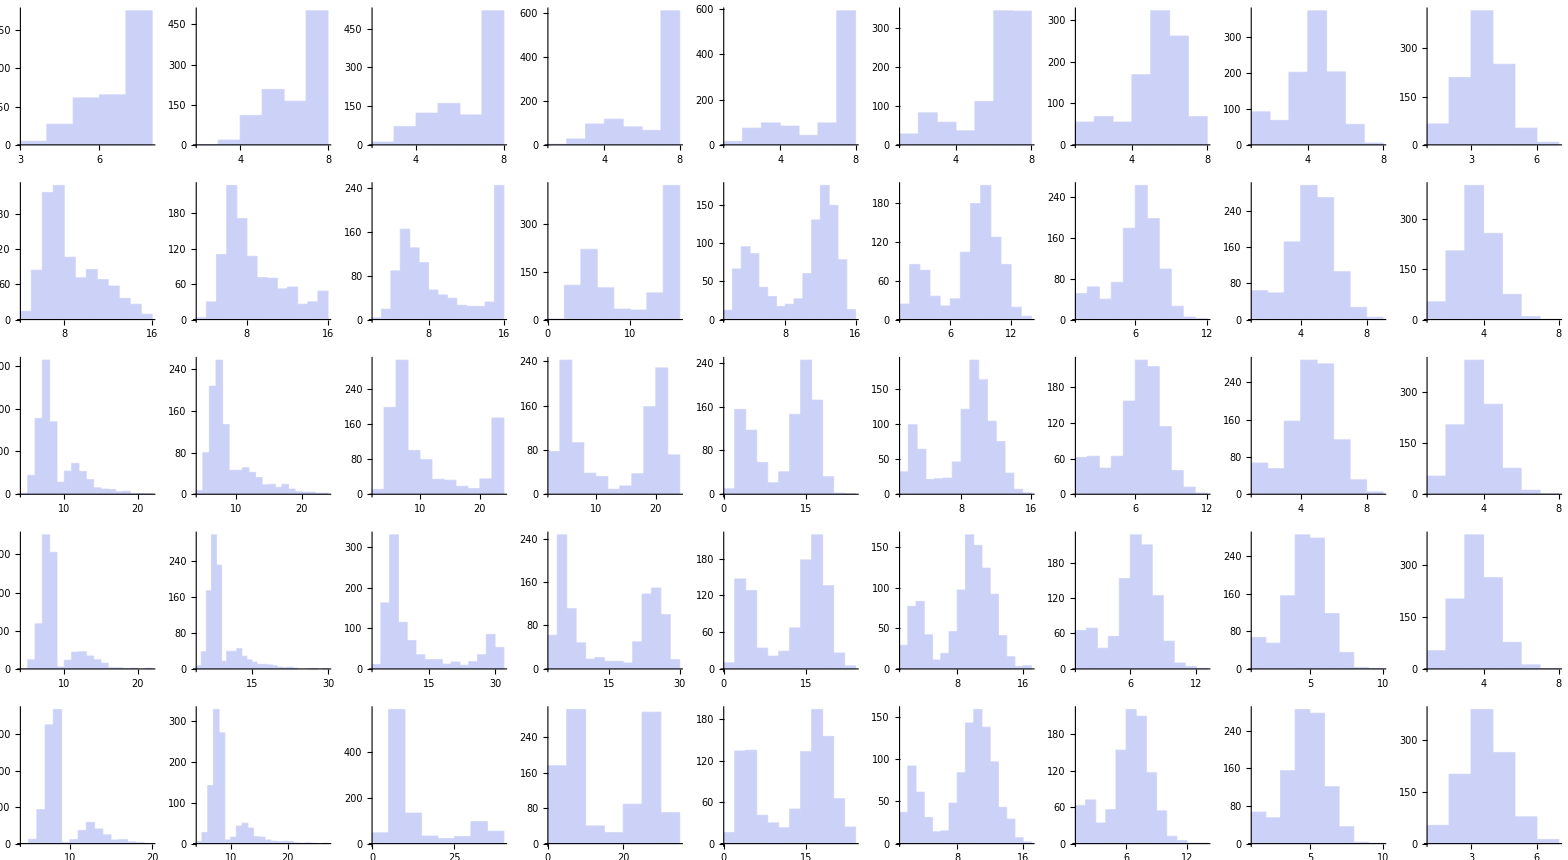

```mathematica
With[{dataframe=data},
GraphicsGrid[Table[
HistogramOfE[m,k,dataframe],
{m,8,40,8},{k,0,4,0.5}]]]
```

```mathematica
Grid[
Table[
With[{m=m,k=k},
Mean[
Map[(#[[1]] * #[[2]] )&,
Map[List[(#⟦1⟧/(m-1)),(#⟦2⟧)] &, 
SelectCols["E","r",data // FilterByCol["m",m,#]& // FilterByCol["k",k,#]&]
]
]
]

]
,
{m,8,40,8},{k,0,4,0.5}]]
```

0.124293 | 0.136031 | 0.195296 | 0.315661 | 0.43741 | 0.541728 | 0.526938 | 0.450911 | 0.38961
0.046098 | 0.0552321 | 0.117303 | 0.235453 | 0.325691 | 0.337548 | 0.291742 | 0.233546 | 0.186984
0.022592 | 0.0296371 | 0.0851879 | 0.202695 | 0.256042 | 0.238865 | 0.192608 | 0.154468 | 0.122713
0.0114764 | 0.0176065 | 0.0705765 | 0.168435 | 0.210395 | 0.180908 | 0.144497 | 0.114909 | 0.0911644
0.00905075 | 0.0116063 | 0.0570933 | 0.144812 | 0.171129 | 0.148022 | 0.115157 | 0.0915169 | 0.0724419

```mathematica
?Mean
```

Mean[list] gives the statistical mean of the elements in list. 
Mean[dist] gives the mean of the symbolic distribution dist.

```mathematica
t=ParallelTable[
With[{m=m,k=k},
Mean[
Map[(#[[1]] * #[[2]] )&,
Map[List[(#⟦1⟧/(m-1)),(#⟦2⟧)] &, 
SelectCols["E","r",data2 // FilterByCol["m",m,#]& // FilterByCol["k",k,#]&]
]
]
]

]
,
{m,2,20,2},{k,0,4,0.5}]
```

```mathematica
t // TableForm
```

0.499852 | 0.517766 | 0.563027 | 0.623326 | 0.678004 | 0.73802 | 0.796861 | 0.850655 | 0.887629
0.255259 | 0.264898 | 0.325607 | 0.412337 | 0.547423 | 0.633063 | 0.729807 | 0.757361 | 0.734451
0.166891 | 0.18694 | 0.234992 | 0.354307 | 0.491444 | 0.587239 | 0.631382 | 0.595193 | 0.516789
0.124293 | 0.136031 | 0.195296 | 0.315661 | 0.43741 | 0.541728 | 0.526938 | 0.450911 | 0.38961
0.0935862 | 0.10778 | 0.169544 | 0.286609 | 0.420982 | 0.476677 | 0.443626 | 0.375414 | 0.307967
0.0747606 | 0.0849726 | 0.14799 | 0.263717 | 0.371221 | 0.414418 | 0.368666 | 0.313067 | 0.253204
0.0558387 | 0.0684571 | 0.132885 | 0.26381 | 0.36669 | 0.374499 | 0.326202 | 0.268501 | 0.21421
0.046098 | 0.0552321 | 0.117303 | 0.235453 | 0.325691 | 0.337548 | 0.291742 | 0.233546 | 0.186984
0.0386529 | 0.0470207 | 0.113461 | 0.222661 | 0.319452 | 0.307593 | 0.260324 | 0.207248 | 0.165317
0.0311458 | 0.0415451 | 0.100656 | 0.206466 | 0.298356 | 0.286694 | 0.234102 | 0.186217 | 0.148307

```mathematica
?ListPlot3D
```

ListPlot3D[array] generates a three-dimensional plot of a surface representing an array of height values. 
ListPlot3D[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}] generates a plot of the surface with heights z_i at positions {x_i,y_i}. 
ListPlot3D[{data_1,data_2,…}] plots the surfaces corresponding to each of the data_i.